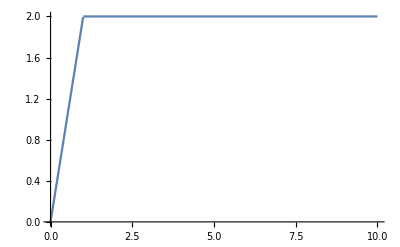

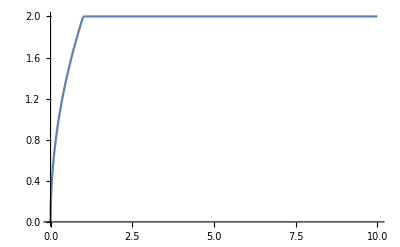

```mathematica
dEuler[x_]:=If[x≤1,2*x,2];
Plot[dEuler[x],{x,0,10}]
Plot[dEuler[Sqrt@x],{x,0,10}]
```

```mathematica
dx=0.01;
xmin=-10;
xmax=10;
diffbox=Table[
xmin=-0.5-d;
xmax=0.5+d;
{d,
Total[Table[(UnitBox[x-d/2]-UnitBox[x+d/2])^2,{x,xmin-dx/2,xmax+dx/2,dx}]]*dx
},{d,0,3,0.1}];
difftriangle=Table[
xmin=-0.5-d;
xmax=0.5+d;
{d,
Total[Table[(UnitTriangle[x-d/2]-UnitTriangle[x+d/2])^2,{x,xmin-dx/2,xmax+dx/2,dx}]]*dx
},{d,0,3,0.1}];
```

```mathematica
xl=Row[{Style["Separation distance between particles Δ",FontFamily->"Latin Modern Roman",Plain,18],Style["r",FontFamily->"Latin Modern Roman",Italic,18]}]
yl=DisplayForm[Row[{Style["Distance ",FontFamily->"Latin Modern Roman",Plain,18],DisplayForm@SuperscriptBox[SubscriptBox[Style["D",FontFamily->"Latin Modern Roman",Plain,18],Style["Euler",FontFamily->"Latin Modern Roman",Plain,12]],Style["2",FontFamily->"Latin Modern Roman",Plain,12]],Style["(Δ",FontFamily->"Latin Modern Roman",Plain,18],
Style["r",FontFamily->"Latin Modern Roman",Italic,18],
Style[")",FontFamily->"Latin Modern Roman",Plain,18]}]]
```

Separation distance between particles Δr

Distance D_Euler^2(Δr)

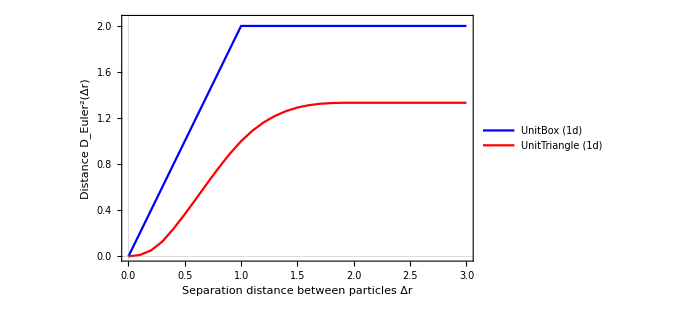

```mathematica
g=ListLinePlot [{diffbox,difftriangle},
AspectRatio->1/GoldenRatio,
PlotStyle->{Blue,Red,Green},
PlotRange->{{0,3},{0,2.05}},
ColorFunctionScaling->False,
PlotTheme->"Scientific",
FrameStyle->Directive[Black,FontColor->Black,15,FontFamily->"Latin Modern Roman",Plain],
FrameLabel->{xl,yl},
PlotLegends->Placed[LineLegend[Automatic,{Style["UnitBox (1d)",16,FontFamily->"Latin Modern Roman",Plain],Style["UnitTriangle (1d)",16,FontFamily->"Latin Modern Roman",Plain]},LegendLayout->"Column"],{4.5/6,0.255}],
ImageSize->{500,500./GoldenRatio},
PlotRangePadding->0]
```

```mathematica
Export["/home/tm/Projects/teatime_presentation/images/unitkernels_1d.png",g,"PNG",ImageResolution->300]
```

/home/tm/Projects/teatime_presentation/images/unitkernels_1d.png

```mathematica
dy=0.01;
ymin=-0.5;
ymax=0.5;
```

```mathematica
diff2=Table[
xmin=-0.5-d;
xmax=0.5+d;
{d,
Total[Flatten@Table[(UnitBox[Sqrt[(x-d/2)^2+y^2]]-UnitBox[Sqrt[(x+d/2)^2+y^2]])^2,{x,xmin-dx/2,xmax-dx/2,dx},{y,ymin-dy/2,ymax+dy/2,dy}]]*dx*dy
},{d,0,3,0.05}];
```

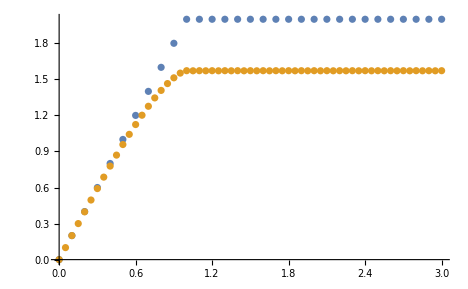

```mathematica
ListPlot [{diff1,diff2},AspectRatio->1/GoldenRatio]
```

```mathematica
dz=0.01;
zmin=-0.5;
zmax=0.5;
```

```mathematica
diff3=Table[
xmin=-0.5-d;
xmax=0.5+d;
{d,
Total[Flatten@Table[(UnitBox[Sqrt[(x-d/2)^2+y^2+z^2]]-UnitBox[Sqrt[(x+d/2)^2+y^2+z^2]])^2,{x,xmin-dx/2,xmax-dx/2,dx},{y,ymin-dy/2,ymax+dy/2,dy},{z,zmin-dz/2,zmax+dz/2,dz}]]*dx*dy*dz
},{d,0,1.2,0.05}];
```

```mathematica
diff3new=Join[diff3,Table[{x,1.047968},{x,1.25,3,0.05}]]
```

{{0.,0.},{0.05,0.078568},{0.1,0.156752},{0.15,0.234072},{0.2,0.310208},{0.25,0.384744},{0.3,0.457392},{0.35,0.527592},{0.4,0.59512},{0.45,0.65924},{0.5,0.720432},{0.55,0.776888},{0.6,0.82984},{0.65,0.877256},{0.7,0.92056},{0.75,0.957336},{0.8,0.989184},{0.85,1.01377},{0.9,1.03275},{0.95,1.04353},{1.,1.04797},{1.05,1.04726},{1.1,1.04797},{1.15,1.04726},{1.2,1.04797},{1.25,1.04797},{1.3,1.04797},{1.35,1.04797},{1.4,1.04797},{1.45,1.04797},{1.5,1.04797},{1.55,1.04797},{1.6,1.04797},{1.65,1.04797},{1.7,1.04797},{1.75,1.04797},{1.8,1.04797},{1.85,1.04797},{1.9,1.04797},{1.95,1.04797},{2.,1.04797},{2.05,1.04797},{2.1,1.04797},{2.15,1.04797},{2.2,1.04797},{2.25,1.04797},{2.3,1.04797},{2.35,1.04797},{2.4,1.04797},{2.45,1.04797},{2.5,1.04797},{2.55,1.04797},{2.6,1.04797},{2.65,1.04797},{2.7,1.04797},{2.75,1.04797},{2.8,1.04797},{2.85,1.04797},{2.9,1.04797},{2.95,1.04797},{3.,1.04797}}

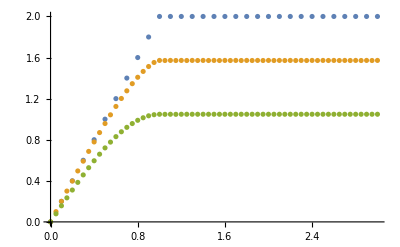

```mathematica
ListPlot [{diff1,diff2,diff3new},AspectRatio->1/GoldenRatio]
```

```mathematica
xl=Row[{Style["Separation distance between particles ",FontFamily->"Latin Modern Roman",Plain,18],Style["l",FontFamily->"Latin Modern Roman",Italic,18],Style[" [m]",FontFamily->"Latin Modern Roman",Plain,18]}]
yl=DisplayForm[Row[{Style["Distance ",FontFamily->"Latin Modern Roman",Plain,18],Style["d(l)",FontFamily->"Latin Modern Roman",Italic,18],Style[" [",FontFamily->"Latin Modern Roman",Plain,18],SuperscriptBox[Style["m",FontFamily->"Latin Modern Roman",Plain,18],Style["dim",FontFamily->"Latin Modern Roman",Plain,12]],Style["]",FontFamily->"Latin Modern Roman",Plain,18]}]]
pl[dim_]:=Row[{DisplayForm[Style["dim",16,FontFamily->"Latin Modern Roman",Plain]],Style["="<>ToString[dim],FontFamily->"Latin Modern Roman",Plain,16]}];
```

Separation distance between particles l [m]

Distance d(l) [m^dim]

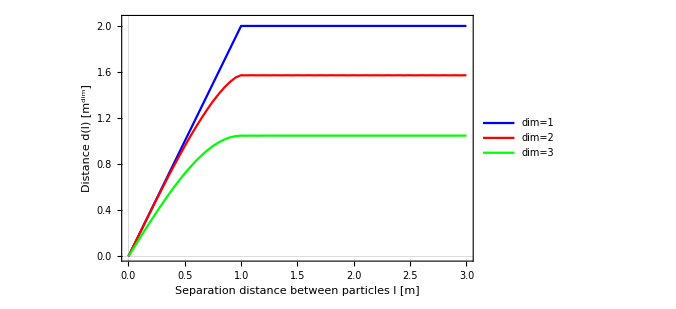

```mathematica
g=ListLinePlot[
{diff1,diff2,diff3new},
PlotStyle->{Blue,Red,Green},
PlotRange->{{0,3},{0,2.05}},
ColorFunctionScaling->False,
PlotTheme->"Scientific",
FrameStyle->Directive[Black,FontColor->Black,15,FontFamily->"Latin Modern Roman",Plain],
FrameLabel->{xl,yl},
PlotLegends->Placed[LineLegend[Automatic,{pl[1],pl[2],pl[3]},LegendLayout->"Column"],{5/6+0.02,0.255}],
ImageSize->{500,500./GoldenRatio},
PlotRangePadding->0
]
```

```mathematica
Export["/home/tm/Projects/teatime_presentation/images/box_filter_distance.png",g,ImageResolution->500];
```